调节能量，根据特征值设置步长

```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
ρ=10^-1;
SIGMA={{1,0},{0,ρ}};
U[xx_,y_]=N[1/2 Simplify[{xx,y}.LinearSolve[SIGMA,{xx,y}]]]
dU[xx_,y_]=GradientG[U[xx,y],{xx,y}]
ddU[xx_,y_]=HessianH[U[xx,y],{xx,y}]
```

0.5 (xx^2+10. y^2)

{1. xx,10. y}

{{1.,0.},{0.,10.}}

```mathematica
x0={0.01,.01};
x=x0;
xs=Table[
g0=Apply[dU,x];
g=LinearSolve[Apply[ddU,x],g0];
δ0=10^-9//N;
δ1=1.;
δ01=(δ1+δ0)/2;
u0=Apply[U,x-δ0 g];
u01=Apply[U,x-δ01 g];
u1=Apply[U,x-δ1 g];
While[Abs[u0-u1]>10^-3,
If[(u0-u01) ( u01-u1)<0,
If[u0<u1,
δ1=δ01,δ0=δ01],
If[u0<u1,δ1=δ01,δ0=δ01]];
δ01=(δ1+δ0)/2;
u0=Apply[U,x-δ0 g];
u01=Apply[U,x-δ01 g];
u1=Apply[U,x-δ1 g]];
g1=Apply[dU,x];
(*Print[g1.LinearSolve[Apply[ddU,x],g1]];*)
x=x-δ01 g(*;
*)(*;Append[x,Apply[U,x-δ01 g]]*),{i,1,10}];
```

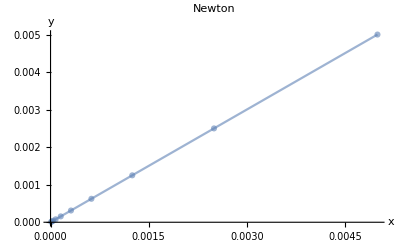

```mathematica
ListLinePlot[xs,PlotMarkers->Automatic,PlotRange->All,PlotStyle->Opacity[0.6],AxesLabel->{"x","y"},PlotLabel->"Newton"]
```